```mathematica
Clear["Global`*"]
```

```mathematica
map[x_,μ_]= μ x(1-x);
map2[x_,μ_]=map[map[x,μ],μ];
map3[x_,μ_]=map[map2[x,μ],μ];
map4[x_,μ_]=map[map3[x,μ],μ];
map5[x_,μ_]=map[map4[x,μ],μ];
map6[x_,μ_]=map[map5[x,μ],μ];
map7[x_,μ_]=map[map6[x,μ],μ];
map8[x_,μ_]=map[map7[x,μ],μ];
map9[x_,μ_]=map[map8[x,μ],μ];
map10[x_,μ_]=map[map9[x,μ],μ];
```

```mathematica
s1=Normal[Series[Simplify[map3[x,μ]], {x,0,3}]]
```

x μ^3+x^2 (-μ^3-μ^4-μ^5)+2 x^3 (μ^4+μ^5+μ^6)

```mathematica
Show[shadows,Plot[0.5,{x,3,4}, PlotStyle->{Black, Thick}],
ListPlot[{listfixedx,listfixedx2,listfixedx3, listfixedx4,listfixedx5,listfixedx6,listfixedx7,listfixedx8,listfixedx9,listfixedx10}, PlotStyle->{{PointSize[0.01],Green},{PointSize[0.005],Red},{PointSize[0.005],Brown},{PointSize[0.005],Yellow},{PointSize[0.005],Orange},{PointSize[0.005],Cyan},{PointSize[0.005],Magenta},{PointSize[0.005],Gray},{PointSize[0.005],Black},{PointSize[0.005],Purple}}],ImageSize-> Large]
```

-Graphics-

x_(n+1)= x_n μ (1 - x_n)

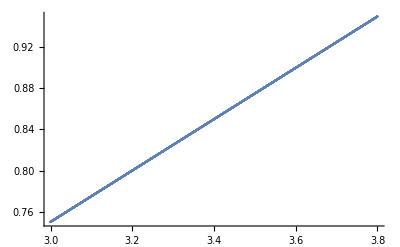

```mathematica
ListPlot[listfixedx]
```

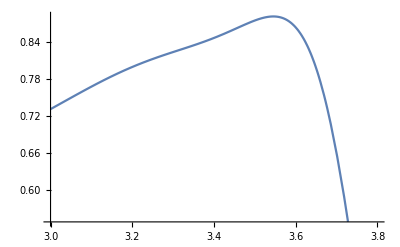

```mathematica
Plot[q5[as],{as,3,3.8}]
```

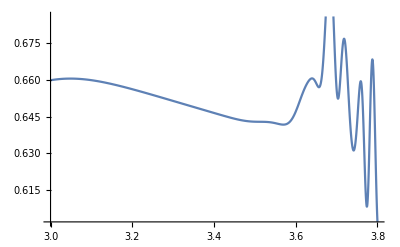

```mathematica
media10[μn] = (q1[μn] + q2[μn]+  q3[μn] + q4[μn]+ q5[μn] + q6[μn]+ q7[μn] + q8[μn]+ q9[μn] + q10[μn])/10;
media[μn] = (q1[μn] + q2[μn]+  q3[μn] + q4[μn]+ q5[μn])/5;
Plot[media10[μn],{μn,3,3.8}]
```

```mathematica
xcond = 0.50;
```

```mathematica
listfixedx = {};
mu = Range[3,4,0.001];
For[i= 0,i<Length[mu] ,i++;
mulocal = mu⟦i⟧;
result = map[xcond,mulocal];
AppendTo[listfixedx,{mulocal,result}]]
q1 = Interpolation[listfixedx];

listfixedx2 = {};
mu = Range[3,4,0.001];
For[i= 0,i<Length[mu] ,i++;
mulocal = mu⟦i⟧;
result = map2[xcond,mulocal];
AppendTo[listfixedx2,{mulocal,result}]]
q2 = Interpolation[listfixedx2];

listfixedx3 = {};
mu = Range[3,4,0.001];
For[i= 0,i<Length[mu] ,i++;
mulocal = mu⟦i⟧;
result = map3[xcond,mulocal];
AppendTo[listfixedx3,{mulocal,result}]]
q3 = Interpolation[listfixedx3];

listfixedx4 = {};
mu = Range[3,4,0.001];
For[i= 0,i<Length[mu] ,i++;
mulocal = mu⟦i⟧;
result = map4[xcond,mulocal];
AppendTo[listfixedx4,{mulocal,result}]]
q4 = Interpolation[listfixedx4];

listfixedx5 = {};
mu = Range[3,3.8,0.001];
For[i= 0,i<Length[mu] ,i++;
mulocal = mu⟦i⟧;
result = map5[xcond,mulocal];
AppendTo[listfixedx5,{mulocal,result}]]
q5 = Interpolation[listfixedx5];

listfixedx6 = {};
mu = Range[3,4,0.001];
For[i= 0,i<Length[mu] ,i++;
mulocal = mu⟦i⟧;
result = map6[xcond,mulocal];
AppendTo[listfixedx6,{mulocal,result}]]
q6= Interpolation[listfixedx6];

listfixedx7 = {};
mu = Range[3,4,0.001];
For[i= 0,i<Length[mu] ,i++;
mulocal = mu⟦i⟧;
result = map7[xcond,mulocal];
AppendTo[listfixedx7,{mulocal,result}]]
q7= Interpolation[listfixedx7];

listfixedx8 = {};
mu = Range[3,4,0.001];
For[i= 0,i<Length[mu] ,i++;
mulocal = mu⟦i⟧;
result = map8[xcond,mulocal];
AppendTo[listfixedx8,{mulocal,result}]]
q8= Interpolation[listfixedx8];

listfixedx9 = {};
mu = Range[3,4,0.001];
For[i= 0,i<Length[mu] ,i++;
mulocal = mu⟦i⟧;
result = map9[xcond,mulocal];
AppendTo[listfixedx9,{mulocal,result}]]
q9= Interpolation[listfixedx9];

listfixedx10 = {};
mu = Range[3,4,0.001];
For[i= 0,i<Length[mu] ,i++;
mulocal = mu⟦i⟧;
result = map10[xcond,mulocal];
AppendTo[listfixedx10,{mulocal,result}]]
q10= Interpolation[listfixedx10];
```

```mathematica
listfixedn = {};
mu = Range[1,3.8,0.001];
For[i=0,i<Length[mu] ,i++;
mulocal = mu⟦i⟧;
xxn = 0.5;
For[n=0,n≤ 8,n++;
xxn = map[xxn,mulocal];
AppendTo[listfixedn,{mulocal, xxn}]]]
```

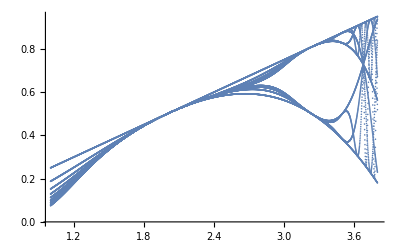

```mathematica
ListPlot[listfixedn]
```

```mathematica
listfixedx = {};
mu = Range[3,3.8,0.0001];
For[i= 0,i<Length[mu] ,i++;
mulocal = mu⟦i⟧;
result = map[xcond,mulocal];
AppendTo[listfixedx,{mulocal,result}]]
```

```mathematica
x = 0.6;
listpointsL = {};
j=1;
For[μ = 3, μ<3.93,μ=μ+0.0001(*0.0000003*),
(*For[i=1,i<100,i++,
x = μ x(1-x)
];*)
AppendTo[listpointsL,{μ}];
For[i=1,i<100,i++,
x =μ x(1-x);
AppendTo[listpointsL⟦j⟧,x];
];
j++;
]
Clear[x,μ];
```

```mathematica
listpointsL
```

{1}
 |  |  |  |

```mathematica
shadows=ListPlot[TemporalData[listpointsL⟦All,2;;⟧,{listpointsL⟦All,1⟧}],PlotStyle->Directive[RGBColor[0.368417, 0.506779, 0.709798],PointSize[0.001]],Frame->True,GridLines->Automatic,ImageSize->Large]
```

-Graphics-

```mathematica
Show[
ListPlot[{listfixedx,listfixedx2,listfixedx3, listfixedx4,listfixedx5}, PlotStyle->{{PointSize[0.01],Green},{PointSize[0.005],Red},{PointSize[0.005],Brown},{PointSize[0.005],Yellow},{PointSize[0.005],Orange}}],shadows,ImageSize-> Large];
```

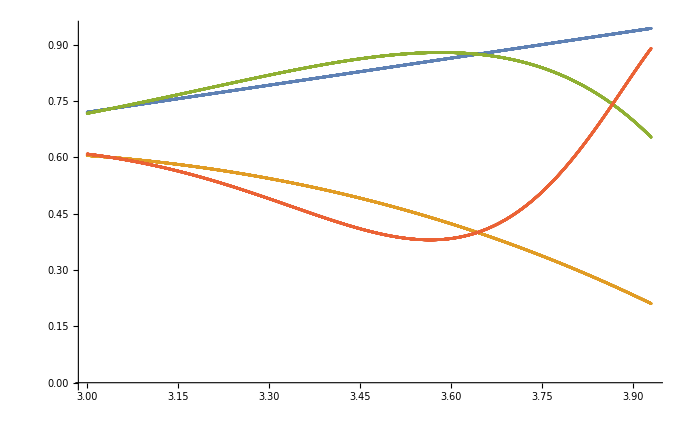

```mathematica
ListPlot[TemporalData[listpointsL⟦All,2;;⟧,{listpointsL⟦All,1⟧}]]
```

```mathematica
listx = Range[0.5,1.0,0.0005];
listy = Range[-0.1,0,0.001];
colourplotsh ={};
For[i=0,i<Length[listy],i++;
localcolourpoints = {};
y = listy⟦i⟧;
For[j=0,j<Length[listx],j++;
x = listx⟦j⟧;
AppendTo[localcolourpoints,{x,y}]];
AppendTo[colourplotsh,localcolourpoints]]
```

```mathematica
listploth={};
For[i=0,i<Length[listy],i++;
ploth=ListPlot[colourplotsh3⟦i⟧,PlotStyle->Hue[i/120]];
AppendTo[listploth,ploth]];
```

```mathematica
listploth={};
For[i=0,i<Length[listy],i++;
ploth=ListPlot[colourplotsh⟦i⟧,PlotStyle->Hue[i/120]];
AppendTo[listploth,ploth]];
```

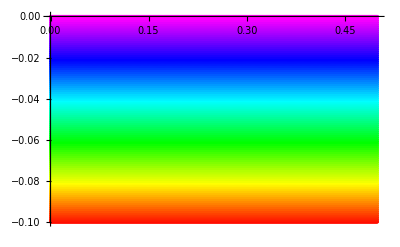

```mathematica
Show[listploth,PlotRange-> Automatic]
```

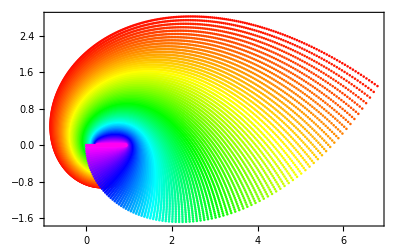

```mathematica
Show[listploth, PlotRange-> Automatic,Frame-> True]
```

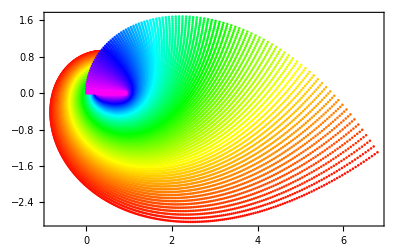

```mathematica
Show[listploth, PlotRange-> Automatic,Frame-> True]
```

```mathematica
Length[listy]
```

1001

```mathematica
colourplotsh3={};
Clear[x]
Clear[y]
μ = 3.7;

xn[x_,y_] = x μ^3-x^2 μ^3+y^2 μ^3-x^2 μ^4+2 x^3 μ^4-x^4 μ^4+y^2 μ^4-6 x y^2 μ^4+6 x^2 y^2 μ^4-y^4 μ^4-x^2 μ^5+2 x^3 μ^5-x^4 μ^5+y^2 μ^5-6 x y^2 μ^5+6 x^2 y^2 μ^5-y^4 μ^5+2 x^3 μ^6-6 x^4 μ^6+6 x^5 μ^6-2 x^6 μ^6-6 x y^2 μ^6+36 x^2 y^2 μ^6-60 x^3 y^2 μ^6+30 x^4 y^2 μ^6-6 y^4 μ^6+30 x y^4 μ^6-30 x^2 y^4 μ^6+2 y^6 μ^6-x^4 μ^7+4 x^5 μ^7-6 x^6 μ^7+4 x^7 μ^7-x^8 μ^7+6 x^2 y^2 μ^7-40 x^3 y^2 μ^7+90 x^4 y^2 μ^7-84 x^5 y^2 μ^7+28 x^6 y^2 μ^7-y^4 μ^7+20 x y^4 μ^7-90 x^2 y^4 μ^7+140 x^3 y^4 μ^7-70 x^4 y^4 μ^7+6 y^6 μ^7-28 x y^6 μ^7+28 x^2 y^6 μ^7-y^8 μ^7;

yn[x_,y_] = y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7;


For[m=0,m<Length[colourplotsh],m++;
localcolourpoints3 = {};
For[n=0,n<Length[colourplotsh⟦m⟧],n++;
xlocal = colourplotsh⟦m,n,1⟧;
ylocal = colourplotsh⟦m,n,2⟧;
{x3 ,y3}= {xn[xlocal,ylocal],yn[xlocal,ylocal]};
AppendTo[localcolourpoints3,{x3,y3}]];
AppendTo[colourplotsh3,localcolourpoints3]]
```

Plot com intervalos reduzidos tentando mostrar comportamento próximo do acúmulo

```mathematica
ListPlot[colourplotsh3,PlotRange->{{0.65,0.75},{-0.008,0.008}}]
```

-Graphics-

Plot com intervalos reduzidos tentando mostrar comportamento próximo do acúmulo

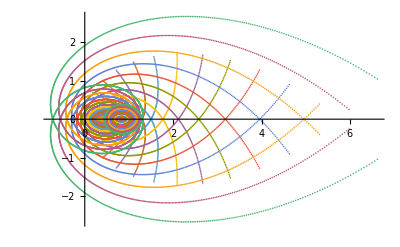

```mathematica
ListPlot[colourplotsh3,PlotRange->All]
```

Plot com intervalo para x [0, 0.5]

```mathematica
ListPlot[colourplotsh3,PlotRange->All]
```

-Graphics-

Plot com intervalo para x [0.5, 1.0]

```mathematica
ListPlot[colourplotsh3, Frame-> True, PlotRange->Automatic]
```

-Graphics-

Plot com intervalo para x [0, 1.0]

```mathematica
ListPlot[colourplotsh3,PlotRange->All]
```

-Graphics-

Plot com intervalo para y [- 0.1, 0] (só negativos)

```mathematica
ListPlot[colourplotsh3,PlotRange->All]
```

-Graphics-

Plot com intervalo para y [0, 0.1] (só positivos)

```mathematica
ListPlot[colourplotsh3,PlotRange->All]
```

-Graphics-

```mathematica
listx = Range[0,1,0.2];
listy = Range[-0.1,0.1,0.0001];
colourplotsv ={};
For[i=0,i<Length[listx],i++;
localcolourpoints = {};
x= listx⟦i⟧;
For[j=0,j<Length[listy],j++;
y = listy⟦j⟧;
AppendTo[localcolourpoints,{x,y}]];
AppendTo[colourplotsv,localcolourpoints]]
```

```mathematica
ListPlot[colourplotsv]
```

-Graphics-

```mathematica
colourplotsv3={};
Clear[x]
Clear[y]
μ = 3.7;

xn[x_,y_] = x μ^3-x^2 μ^3+y^2 μ^3-x^2 μ^4+2 x^3 μ^4-x^4 μ^4+y^2 μ^4-6 x y^2 μ^4+6 x^2 y^2 μ^4-y^4 μ^4-x^2 μ^5+2 x^3 μ^5-x^4 μ^5+y^2 μ^5-6 x y^2 μ^5+6 x^2 y^2 μ^5-y^4 μ^5+2 x^3 μ^6-6 x^4 μ^6+6 x^5 μ^6-2 x^6 μ^6-6 x y^2 μ^6+36 x^2 y^2 μ^6-60 x^3 y^2 μ^6+30 x^4 y^2 μ^6-6 y^4 μ^6+30 x y^4 μ^6-30 x^2 y^4 μ^6+2 y^6 μ^6-x^4 μ^7+4 x^5 μ^7-6 x^6 μ^7+4 x^7 μ^7-x^8 μ^7+6 x^2 y^2 μ^7-40 x^3 y^2 μ^7+90 x^4 y^2 μ^7-84 x^5 y^2 μ^7+28 x^6 y^2 μ^7-y^4 μ^7+20 x y^4 μ^7-90 x^2 y^4 μ^7+140 x^3 y^4 μ^7-70 x^4 y^4 μ^7+6 y^6 μ^7-28 x y^6 μ^7+28 x^2 y^6 μ^7-y^8 μ^7;

yn[x_,y_] = y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7;


For[m=0,m<Length[colourplotsv],m++;
localcolourpoints3 = {};
For[n=0,n<Length[colourplotsv⟦m⟧],n++;
xlocal = colourplotsv⟦m,n,1⟧;
ylocal = colourplotsv⟦m,n,2⟧;
{x3 ,y3}= {xn[xlocal,ylocal],yn[xlocal,ylocal]};
AppendTo[localcolourpoints3,{x3,y3}]];
AppendTo[colourplotsv3,localcolourpoints3]]
```

```mathematica
ListPlot[colourplotsv3]
```

-Graphics-

```mathematica
Show[ListPlot[colourplotsv3],ListPlot[colourplotsh3]]
```

-Graphics-

```mathematica
colourplotsv1={};
Clear[x]
Clear[y]
μ = 3.7;

xn[x_,y_] = x μ-x^2 μ+y^2 μ;

yn[x_,y_] = y μ-2 x y μ;

For[m=0,m<Length[colourplotsv],m++;
localcolourpoints1 = {};
For[n=0,n<Length[colourplotsv⟦m⟧],n++;
xlocal = colourplotsv⟦m,n,1⟧;
ylocal = colourplotsv⟦m,n,2⟧;
{x1 ,y1}= {xn[xlocal,ylocal],yn[xlocal,ylocal]};
AppendTo[localcolourpoints1,{x1,y1}]];
AppendTo[colourplotsv1,localcolourpoints1]]
```

```mathematica
ListPlot[colourplotsv1]
```

-Graphics-

```mathematica
colourplotsh1={};
Clear[x]
Clear[y]
μ = 3.7;

xn[x_,y_] = x μ-x^2 μ+y^2 μ;

yn[x_,y_] = y μ-2 x y μ;


For[m=0,m<Length[colourplotsh],m++;
localcolourpoints1 = {};
For[n=0,n<Length[colourplotsh⟦m⟧],n++;
xlocal = colourplotsh⟦m,n,1⟧;
ylocal = colourplotsh⟦m,n,2⟧;
{x1 ,y1}= {xn[xlocal,ylocal],yn[xlocal,ylocal]};
AppendTo[localcolourpoints1,{x1,y1}]];
AppendTo[colourplotsh1,localcolourpoints1]]
```

```mathematica
ListPlot[colourplotsh1]
```

-Graphics-

```mathematica
Show[ListPlot[colourplotsh1],ListPlot[colourplotsv1]]
```

-Graphics-

```mathematica
colourplotsv2={};
Clear[x]
Clear[y]
μ = 3.7;

xn[x_,y_] = x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;

yn[x_,y_] =y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;

For[m=0,m<Length[colourplotsv],m++;
localcolourpoints2 = {};
For[n=0,n<Length[colourplotsv⟦m⟧],n++;
xlocal = colourplotsv⟦m,n,1⟧;
ylocal = colourplotsv⟦m,n,2⟧;
{x2 ,y2}= {xn[xlocal,ylocal],yn[xlocal,ylocal]};
AppendTo[localcolourpoints2,{x2,y2}]];
AppendTo[colourplotsv2,localcolourpoints2]]
```

```mathematica
ListPlot[colourplotsv2]
```

-Graphics-

```mathematica
colourplotsh2={};
Clear[x]
Clear[y]
μ = 3.7;

xn[x_,y_] =x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;

yn[x_,y_] = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;


For[m=0,m<Length[colourplotsh],m++;
localcolourpoints2 = {};
For[n=0,n<Length[colourplotsh⟦m⟧],n++;
xlocal = colourplotsh⟦m,n,1⟧;
ylocal = colourplotsh⟦m,n,2⟧;
{x2 ,y2}= {xn[xlocal,ylocal],yn[xlocal,ylocal]};
AppendTo[localcolourpoints2,{x2,y2}]];
AppendTo[colourplotsh2,localcolourpoints2]]
```

```mathematica
ListPlot[colourplotsh2]
```

-Graphics-

```mathematica
Show[ListPlot[colourplotsh2],ListPlot[colourplotsv2]]
```

-Graphics-

```mathematica
listx = Range[0,1.0,0.1];
listy = Range[-0.1,0.1,0.05];
listsize =Range[0,1.0,0.1];
colourplotsh ={};
For[i=0,i<Length[listy],i++;
localcolourpoints = {};
y = listy⟦i⟧;
For[j=0,j<Length[listx],j++;
x = listx⟦j⟧;
AppendTo[localcolourpoints,{x,y}]];
AppendTo[colourplotsh,localcolourpoints]]
```

```mathematica
Clear[i,j];
listadeplots ={};
For[i=0, i≤ 0.1,i=i+0.05,
For[j=0,j≤ 1,j=j+0.2,
plotlocal = ListPlot[{{j,i}},PlotStyle->{PointSize[j/10],Hue[j]}];
AppendTo[listadeplots, plotlocal]]]
```

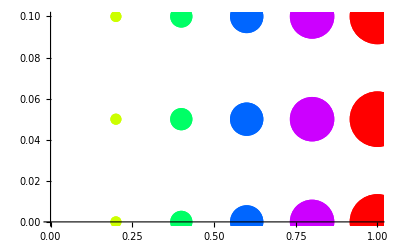

```mathematica
Show[listadeplots,PlotRange-> All]
```

```mathematica
xn[x_,y_] = x μ^3-x^2 μ^3+y^2 μ^3-x^2 μ^4+2 x^3 μ^4-x^4 μ^4+y^2 μ^4-6 x y^2 μ^4+6 x^2 y^2 μ^4-y^4 μ^4-x^2 μ^5+2 x^3 μ^5-x^4 μ^5+y^2 μ^5-6 x y^2 μ^5+6 x^2 y^2 μ^5-y^4 μ^5+2 x^3 μ^6-6 x^4 μ^6+6 x^5 μ^6-2 x^6 μ^6-6 x y^2 μ^6+36 x^2 y^2 μ^6-60 x^3 y^2 μ^6+30 x^4 y^2 μ^6-6 y^4 μ^6+30 x y^4 μ^6-30 x^2 y^4 μ^6+2 y^6 μ^6-x^4 μ^7+4 x^5 μ^7-6 x^6 μ^7+4 x^7 μ^7-x^8 μ^7+6 x^2 y^2 μ^7-40 x^3 y^2 μ^7+90 x^4 y^2 μ^7-84 x^5 y^2 μ^7+28 x^6 y^2 μ^7-y^4 μ^7+20 x y^4 μ^7-90 x^2 y^4 μ^7+140 x^3 y^4 μ^7-70 x^4 y^4 μ^7+6 y^6 μ^7-28 x y^6 μ^7+28 x^2 y^6 μ^7-y^8 μ^7;

yn[x_,y_] = y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7;
```

```mathematica
Clear[i,j];
listadeplots ={};
μ=3.7
For[i=0, i≤ 0.1,i=i+0.05,
For[j=0,j≤ 1,j=j+0.2,
plotlocal = ListPlot[{{xn[j,i],yn[j,i]}},PlotStyle->{PointSize[j/10],Hue[j]}];
AppendTo[listadeplots, plotlocal]]]
```

3.7

```mathematica
xn[0.5,0.5]
```

0.5 μ^3-0.25 μ^4-0.25 μ^5+0.25 μ^6-0.0625 μ^7

```mathematica
Show[listadeplots,PlotRange-> All]
```

-Graphics-

```mathematica
lista⟦1⟧
ListPlot[lista⟦5⟧]
```

{{0,1},{1,2},{2,3},{3,4},{4,5}}

-Graphics-

```mathematica
2{{0,1},{1,2},{2,3},{3,4}}
```

{{0,2},{2,4},{4,6},{6,8}}